```mathematica
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]];
If[!MemberQ[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]],AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]]];
Print["Package path ",FindFile["GDCComparisons`"]];
Print["Package path ",FindFile["GDCAnalysis3`"]];
<<GDCAnalysis3`
<<GDCComparisons`
```

Package path /home/carla/GDC/DialecticalStructures/GDCComparisons.m

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis3.m

```mathematica
filesAR=FileNames["/home/carla/GDC/CH_Pool/LYE/GDC_CHP_AR_LYE_ALL_Out/*.txt"];
inputAR=Map[Get[#]&, filesAR];
dojAR=inputAR[[All,1]];
zAR=inputAR[[All,2]];
fAR=inputAR[[All,3]];
filesBR=FileNames["/home/carla/GDC/CH_Pool/LYE/GDC_CHP_BR_LYE_ALL_Out/*.txt"];
inputBR=Map[Get[#]&, filesBR];
dojBR=inputBR[[All,1]];
zBR=inputBR[[All,2]];
fBR=inputBR[[All,3]];
```

```mathematica
(*MIN Values*)
Map[dojBR[[#]][[1]][["value"]]&,Range[Length[fBR]]]
Map[zBR[[#]][[1]][["value"]]&,Range[Length[fBR]]]
Map[fBR[[#]][[1]][["value"]]&,Range[Length[fBR]]]
```

{0.,0.,0.,0.,0.,0.,DOJ ist nicht definiert! Division durch Null! }

{-1,-1,-1,-1,-1,-1, z ist nicht definiert }

{-1,-1,-1,-1,-1,-1, f ist nicht definiert }

```mathematica
tsAR={1,2,3,4,5,6,7,8};
tsBR={1.5,2.5,3.5,4.5,5.5,6.5,7.5};
tsAll=Union[tsAR,tsBR];
```

```mathematica
dojMax=maxValFunc[tsAR, Drop[tsBR,-1], dojAR, Drop[dojBR,-1], "LYE", "DOJ"]
zMax=maxValFunc[tsAR, Drop[tsBR,-1], dojAR, Drop[dojBR,-1], "LYE", "Z"]
fMax=maxValFunc[tsAR, Drop[tsBR,-1], dojAR, Drop[dojBR,-1], "LYE", "F"]
```

{{1,0.00192891},{1.5,0.00192891},{2,0.00192891},{2.5,0.00192891},{3,0.0105263},{3.5,0.0105263},{4,0.0125},{4.5,0.0153257},{5,0.0108696},{5.5,0.0149254},{6,0.0222222},{6.5,0.0222222},{7,1.},{8,1.}}

{{1,0.00192891},{1.5,0.00192891},{2,0.00192891},{2.5,0.00192891},{3,0.0105263},{3.5,0.0105263},{4,0.0125},{4.5,0.0153257},{5,0.0108696},{5.5,0.0149254},{6,0.0222222},{6.5,0.0222222},{7,1.},{8,1.}}

{{1,0.00192891},{1.5,0.00192891},{2,0.00192891},{2.5,0.00192891},{3,0.0105263},{3.5,0.0105263},{4,0.0125},{4.5,0.0153257},{5,0.0108696},{5.5,0.0149254},{6,0.0222222},{6.5,0.0222222},{7,1.},{8,1.}}

```mathematica
dojTat=Get["/home/carla/GDC/CONF/LYE/LYE_DOJ.txt"]
zTat=Get["/home/carla/GDC/CONF/LYE/LYE_Z.txt"]
fTat=Get["/home/carla/GDC/CONF/LYE/LYE_F.txt"]
```

{{1,0.000275558},{1.5,0.000275558},{2,0.000275558},{2.5,0.000275558},{3,0.00526316},{3.5,0.00526316},{4,0.00625},{4.5,0.00383142},{5,0.00543478},{5.5,0.0021322},{6,0.0222222},{6.5,0.0222222},{7,1.},{8,1.}}

{{1,0.0000308574},{1.5,0.0000450794},{2,0.0000450794},{2.5,0.0000539657},{3,0.00501436},{3.5,0.00502389},{4,0.00601097},{4.5,0.00369636},{5,0.00529995},{5.5,0.00207831},{6,0.0221694},{6.5,0.02217},{7,1.},{8,1.}}

{{1,0.0593116},{1.5,0.0890832},{2,0.0890832},{2.5,0.10855},{3,0.909724},{3.5,0.913032},{4,0.926328},{4.5,0.931902},{5,0.951581},{5.5,0.950701},{6,0.995259},{6.5,0.995315},{7,1},{8,1}}

```mathematica
(*dojPlot=ListLogPlot[{dojMax,dojTat},PlotLegends->{"MAX", "LYE"},PlotStyle->{Red, Blue},PlotLabel->"DOJ : CH=MAX vs. CH=LYE geg EV&BK=LYE",PlotMarkers->{{"X",12}, {"L",12}},ImageSize->400];
zPlot=ListLogPlot[{dojMax,dojTat},PlotLegends->{"MAX", "LYE"},PlotStyle->{Red, Blue},PlotLabel->"Z : CH-MAX vs. CH_LYE geg EV&BK=LYE",PlotMarkers->{{"X",12}, {"L",12}},ImageSize->400];
fPlot=ListLogPlot[{fMax,fTat},PlotLegends->{"MAX", "LYE"},PlotStyle->{Red, Blue},PlotLabel->"F : CH-MAX vs. CH_LYE geg EV&BK=LYE",PlotMarkers->{{"X",12}, {"L",12}},ImageSize->400];
confMAX=Column[{dojPlot,zPlot,fPlot}]*)
```

```mathematica
(* dojBR[[5,2]][["value"]]
dojTat[[10]]
dojBR[[5,2]][["list"]][[1;;3]]
Map[compCHMaxFunc[First[persMixFunc["LYE"]], #, tatCH , dojBR]&,{4.5}]
Map[vvPosFunc[First[persMixFunc["LYE"]],# , tatCH, "CH", "PEN"]&,{4.5}]
Map[vvPosFunc[First[persMixFunc["LYE"]],# , dojBR,  "CH", "PEN"]&,{4.5}]*)
```

```mathematica
tatCH=Map[Get[#]&,FileNames["/home/carla/GDC/POS/*.txt"]];
persInd=First[persMixFunc["LYE"]]
pers="LYE";
```

9

```mathematica
(*VV-Value von CH-TAT : Ähnlichkeit von CH-TAT mit DEV*)
Map[{#,vvPosFunc[persInd,# , tatCH, "CH", "PEN"]}&,{1,2,3,4,5,6,7,8}]
```

{{1,0.733333},{2,0.733333},{3,0.666667},{4,0.666667},{5,0.666667},{6,0.8},{7,1.},{8,1.}}

```mathematica
(*Veritistic Value von CH-MAX : Ähnlichkeit von CH_MAX mit DEV*)
dojVV=vvCHMaxFunc[tsAR, tsBR, dojAR, dojBR,pers];
zVV=vvCHMaxFunc[tsAR, tsBR, zAR, zBR,pers];
fVV=vvCHMaxFunc[tsAR, tsBR, fAR, fBR,pers];
dojVVHist=vvHistPointsFunc[dojVV];
zVVHist=vvHistPointsFunc[zVV];
fVVHist=vvHistPointsFunc[fVV];
```

14

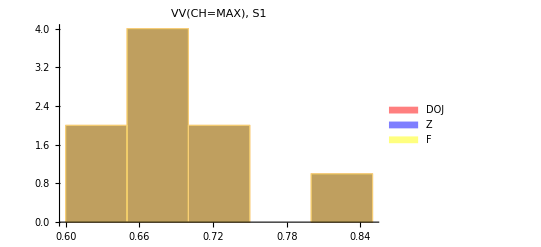
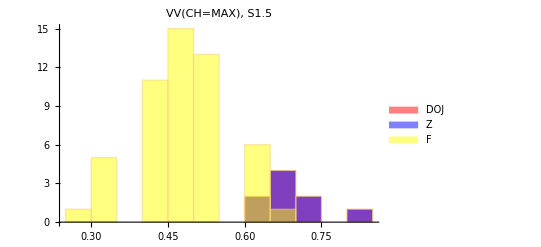
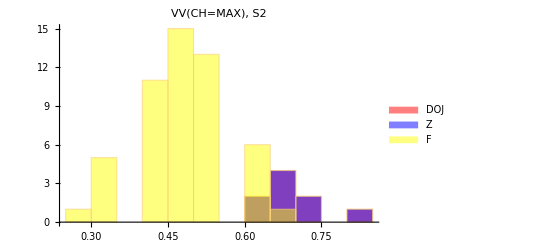
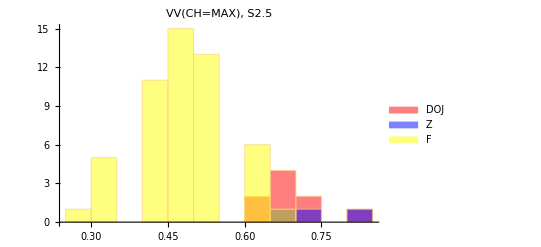
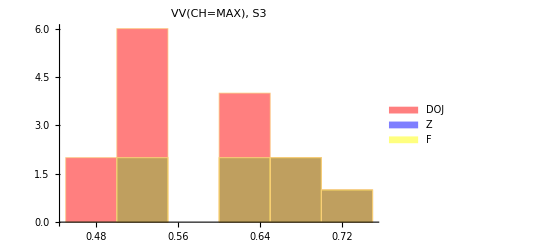
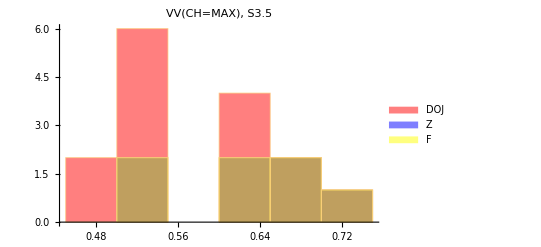
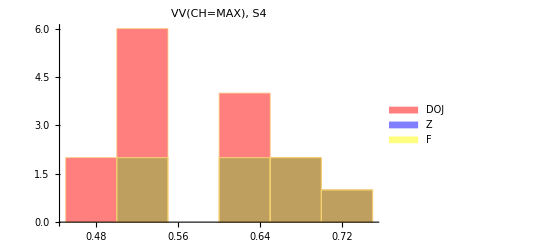
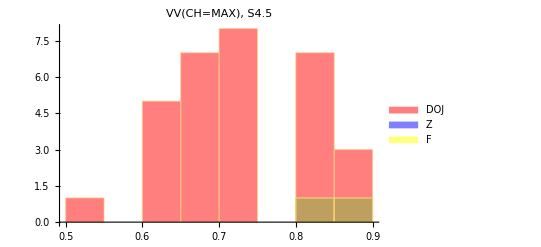
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
(*ListPlot[dojVVHist,PlotLegends->{"DOJ"},PlotStyle->{Red},PlotLabel->"VV CH=MAX geg EV&BK=LYE",PlotMarkers->{{"D",12}}, PlotRange->{0,1.05}]
ListPlot[zVVHist, PlotLegends->{"Z"},PlotStyle->{Blue},PlotLabel->"VV CH=MAX geg EV&BK=LYE",PlotMarkers->{{"Z",12}}, PlotRange->{0,1.05}]
ListPlot[fVVHist, PlotLegends->{"F"},PlotStyle->{Green},PlotLabel->"VV CH=MAX geg EV&BK=LYE",PlotMarkers->{{"F",12}}, PlotRange->{0,1.05}]
vvMaxPlot=ListPlot[{dojVVHist,zVVHist,fVVHist}, PlotLegends->{"DOJ","Z","F"},PlotStyle->{Red,Blue,Green},PlotLabel->"VV CH=MAX geg EV&BK=LYE",PlotMarkers->{{"D",12},{"Z",12},{"F",12}}, PlotRange->{0,1.05}]*)
timL={1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,8};
Length[timL]
hist=Map[Histogram[{dojVV[[#,2]],zVV[[#,2]],fVV[[#,2]]}, PlotLabel->"VV(CH=MAX),    S"<>ToString[timL[[#]]],ImageSize->400, ChartLegends->{"DOJ","Z","F"},ChartStyle->{Red,Blue,Yellow}]&,Range[Length[timL]]];
histOut=Grid[{hist[[1;;3]],hist[[4;;6]],hist[[7;;9]],hist[[10;;12]],hist[[13;;14]]},ItemSize->35]
```

```mathematica
{dojVV[[14,2]],zVV[[14,2]],fVV[[14,2]]}
```

{{1.},{1.},{1.}}

```mathematica
SetDirectory["/home/carla/GDC/CH_Pool/LYE/"];
(*Export["COMP_DOJ_CHTAT_CHMAX_LYE.jpeg",dojPlot,ImageResolution->300]
Export["COMP_CHTAT_CHMAX_LYE.jpeg",confMAX,ImageResolution->300]*)
Put[dojVVHist, "gdc_DOJ_VV_CHMAX_LYE.txt"]
Put[zVVHist, "gdc_Z_VV_CHMAX_LYE.txt"]
Put[fVVHist, "gdc_F_VV_CHMAX_LYE.txt"]
Export["VV_CHMAX_HIST_LYE.jpeg",histOut,ImageResolution->300]
```

VV_CHMAX_HIST_LYE.jpeg